```mathematica
(* Methods used here all from the material of Marini, 1998， Evolutiong from BCS superconductivity to Bose condensation: analytic results for the crossover in three dimensions*)
```

```mathematica
(*Firstly we try calculate directly the two equations for GAP and NUMBER, according to the original expressions, with most traditional methods in mma*)
```

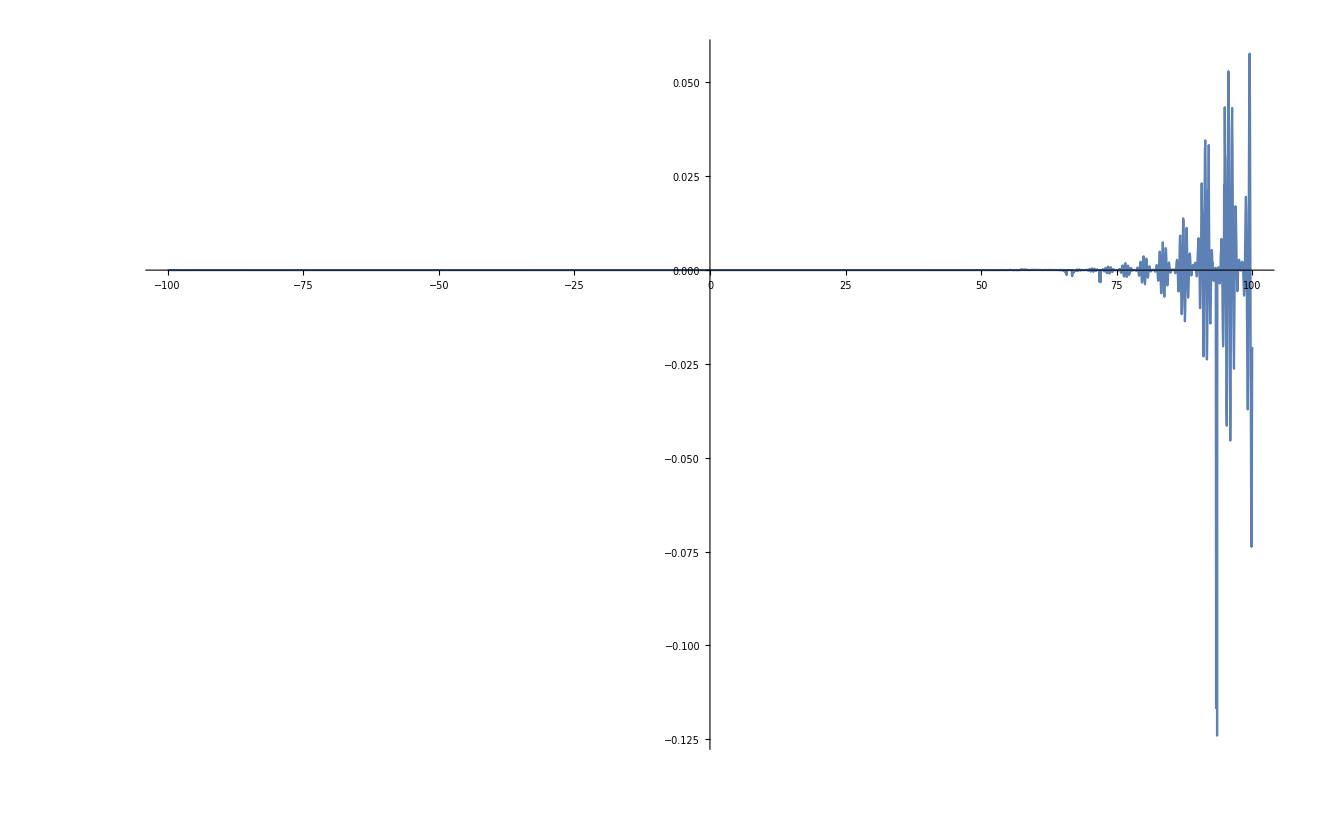

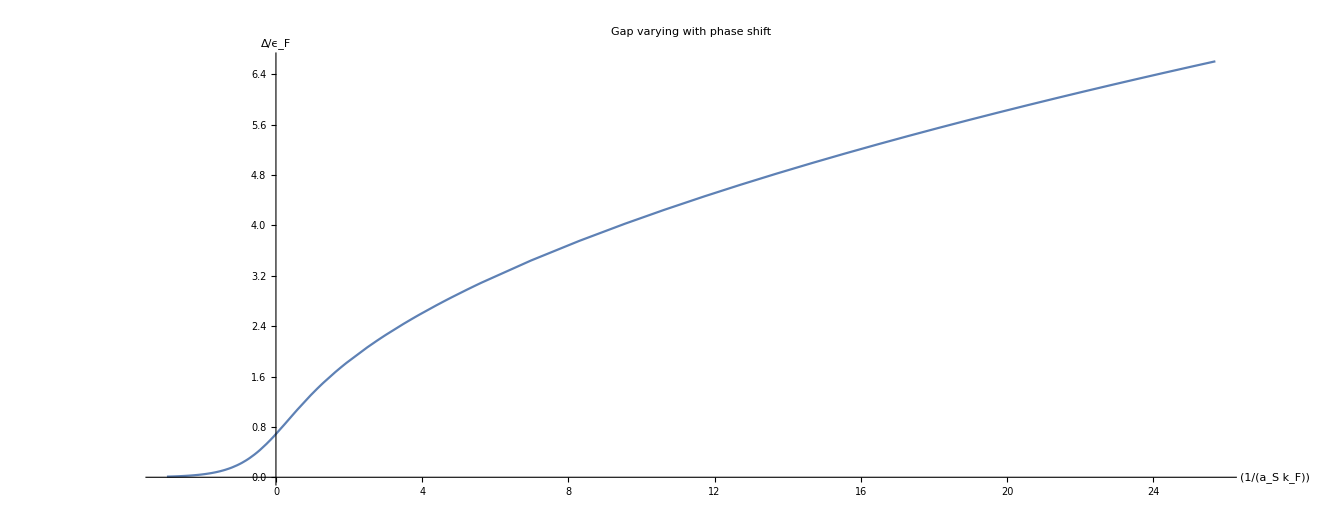

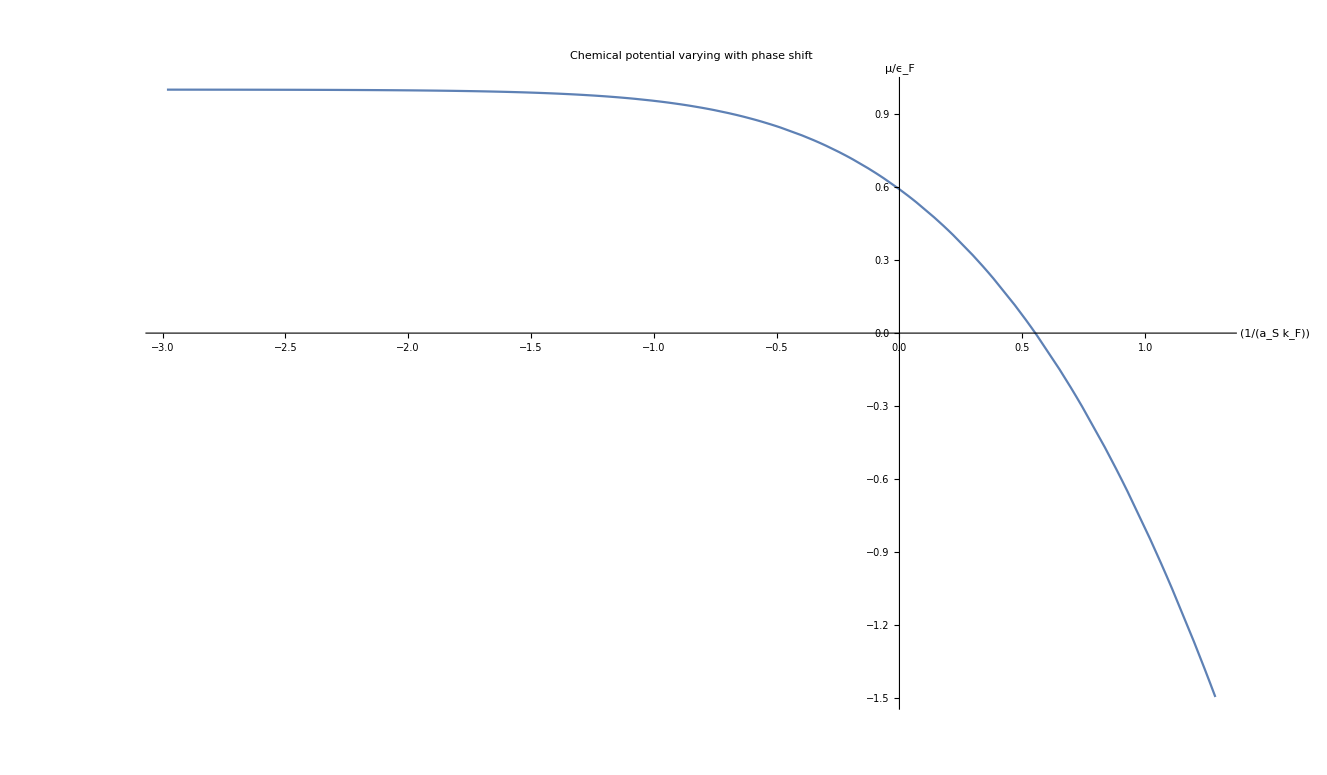

```mathematica
ClearAll["Global`*"];
ξ[x_,x0_]:=x^2-x0;(* Note: x0 for the ratio between chemical potential and energy gap, i.e. x0 = μ/Δ; x^2 stands for the gap only, dimensionless k^2/2mΔ *)
EE[x_,x0_]:=Sqrt[ξ[x,x0]^2+1];
I1[x0_]:=NIntegrate[x^2 (1/EE[x,x0] - 1/x^2),{x,0,∞}] ;
I2[x0_]:=NIntegrate[x^2 (1-ξ[x,x0]/EE[x,x0]),{x,0,∞}];
kainv[x0_]:=-(2/3.1415926)*((2/(3*I2[x0]))^(1/3))*I1[x0];

(*Using Elliptic integral to express the result*)
x1sq[x0_]:=(Sqrt[1+x0^2]+x0)/2;
κsq[x0_]:=x1sq[x0]/Sqrt[1+x0^2];
κ[x0_]:=Sqrt[κsq[x0]];
(*NOTE: here in Mathematica elliptic integrals F(α,κ)=∫_0^α dϕ(1-κ sin^2 ϕ)^-1/2, others similarly *)
I5[x0_]:=NIntegrate[x^2/EE[x,x0]^3,{x,0,∞}];
I5ell[x0_]:=(1+x0^2)^(1/4)EllipticE[Pi/2,κsq[x0]]-(1/(4 x1sq[x0](1+x0^2)^(1/4)))EllipticF[Pi/2,κsq[x0]];
I6[x0_]:=0.5*NIntegrate[(x^4-2x0 x^2+x0^2+1)^(-1/2),{x,0,∞}];
I6ell[x0_]:=0.5(1+x0^2)^(-1/4)EllipticF[Pi/2,κsq[x0]];
err6[x0_]:=100*(I6[x0]/I6ell[x0] -1);
err5[x0_]:=100*(I5[x0]/I5ell[x0] -1);
gap[x0_]:=(x0 I5ell[x0]+I6ell[x0])^(-2/3);
mu[x0_]:=x0*gap[x0];
kfas[x0_]:=-(4/Pi)(x0*I6ell[x0]-I5ell[x0])(x0 I5ell[x0]+I6ell[x0])^(-1/3);
gapas[x0_]:={kfas[x0],gap[x0]};
muas[x0_]:={kfas[x0],mu[x0]};

Plot[err5[x0],{x0,-100,100},PlotRange->Full]

ParametricPlot[gapas[x0],{x0,-100,100},PlotRange->Full,PlotLabel->"Gap varying with phase shift",LabelStyle->Black,AxesLabel->{{1}/{{Subscript[k, F]}{Subscript[a, S]}},Δ/Subscript[ϵ, F]}]
ParametricPlot[muas[x0],{x0,-1,100},PlotRange->All,PlotLabel->"Chemical potential varying with phase shift",LabelStyle->Black,AxesLabel->{{1}/{{Subscript[k, F]}{Subscript[a, S]}},μ/Subscript[ϵ, F]}]
```